```mathematica
data=Import["C:\\Users\\Owner\\Documents\\MOSES\\CrowbarData.xlsx"];
```

```mathematica
pre=data[[1,2,{2,3,4,5,6,7,8,9,10}]];
pimi=data[[1,3,{2,3,4,5,6,7,8,9,10}]];
pipl=data[[1,4,{2,3,4,5,6,7,8,9,10}]];
puup=data[[1,5,{2,3,4,5,6,7,8,9,10}]];
pudn=data[[1,6,{2,3,4,5,6,7,8,9,10}]];
puymi=data[[1,7,{2,3,4,5,6,7,8,9,10}]];
puypl=data[[1,8,{2,3,4,5,6,7,8,9,10}]];
pnd=data[[1,9,{2,3,4,5,6,7,8,9,10}]];
```

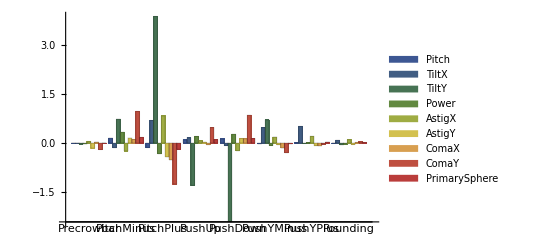

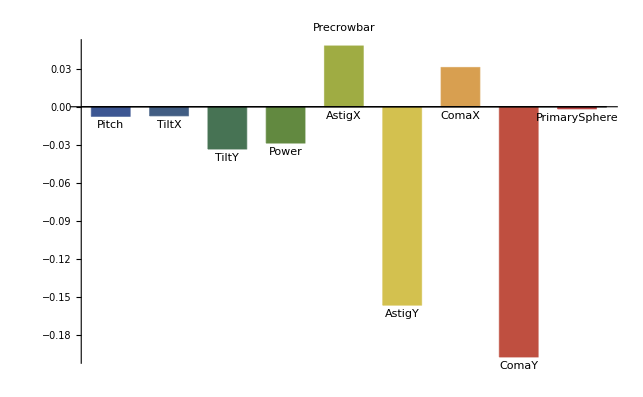

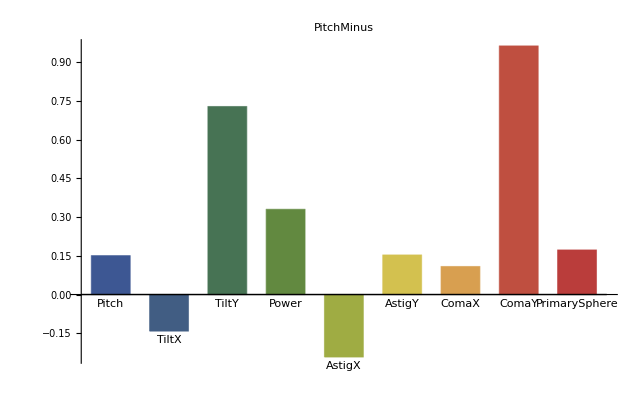

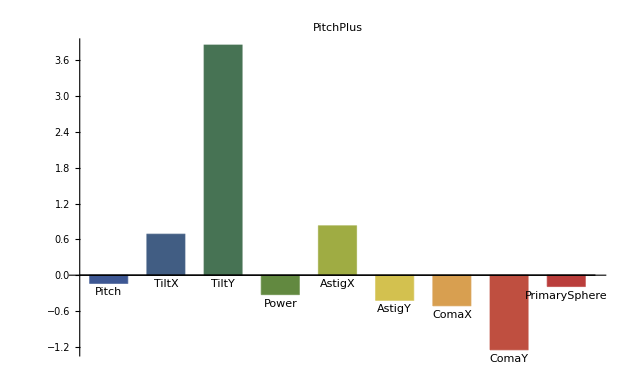

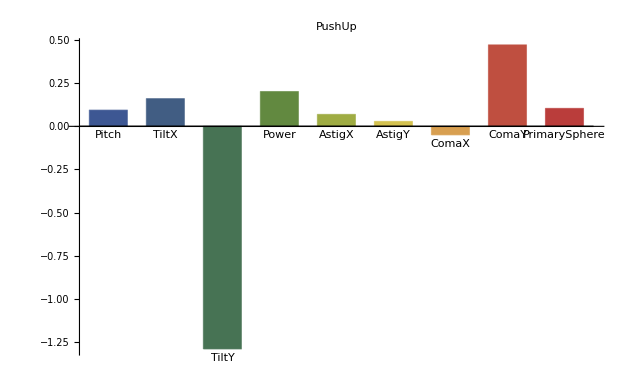

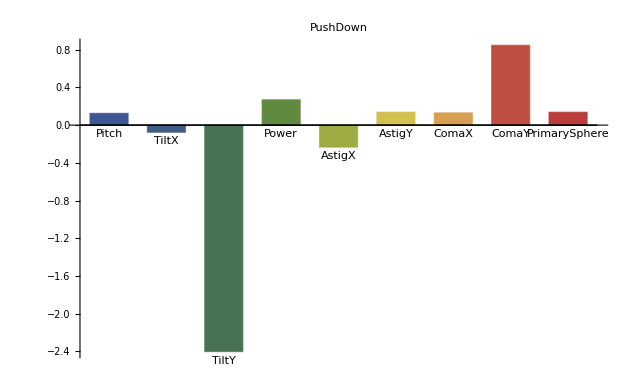

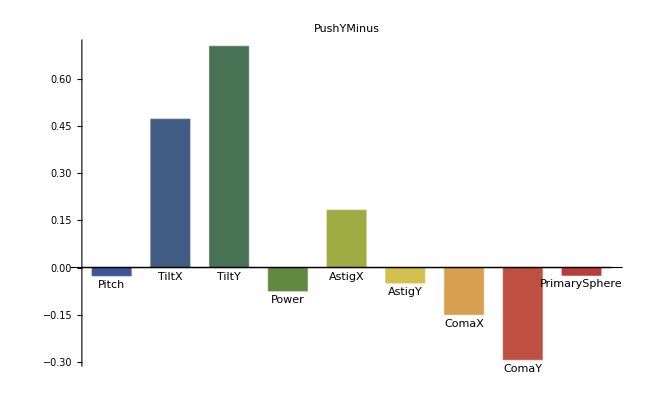

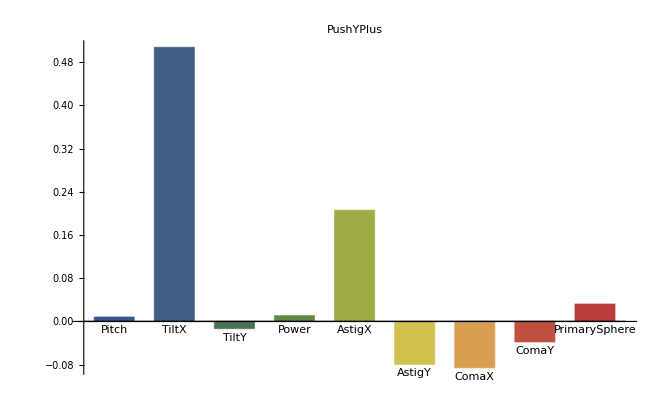

```mathematica
BarChart[{pre,pimi,pipl,puup,pudn,puymi,puypl,pnd},ChartLegends->{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},ChartStyle->"DarkRainbow",ChartLabels->{{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},None},BarSpacing->{Automatic,.7}]
BarChart[pre,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"Precrowbar",BarSpacing->Large]
BarChart[pimi,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"PitchMinus",BarSpacing->Large]
BarChart[pipl,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"PitchPlus",BarSpacing->Large]
BarChart[puup,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"PushUp",BarSpacing->Large]
BarChart[pudn,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"PushDown",BarSpacing->Large]
BarChart[puymi,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"PushYMinus",BarSpacing->Large]
BarChart[puypl,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"PushYPlus",BarSpacing->Large]
BarChart[pnd,ChartLabels->Placed[{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},Below],ChartStyle->"DarkRainbow",PlotLabel->"Pounding",BarSpacing->Large]
```

```mathematica
transdata=Import["C:\\Users\\Owner\\Documents\\MOSES\\CrowbarDataTransposed.xlsx"];
```

```mathematica
pi=transdata[[1,2,{2,3,4,5,6,7,8,9}]];
tx=transdata[[1,3,{2,3,4,5,6,7,8,9}]];
ty=transdata[[1,4,{2,3,4,5,6,7,8,9}]];
pw=transdata[[1,5,{2,3,4,5,6,7,8,9}]];
ax=transdata[[1,6,{2,3,4,5,6,7,8,9}]];
ay=transdata[[1,7,{2,3,4,5,6,7,8,9}]];
cx=transdata[[1,8,{2,3,4,5,6,7,8,9}]];
cy=transdata[[1,9,{2,3,4,5,6,7,8,9}]];
ps=transdata[[1,10,{2,3,4,5,6,7,8,9}]];
```

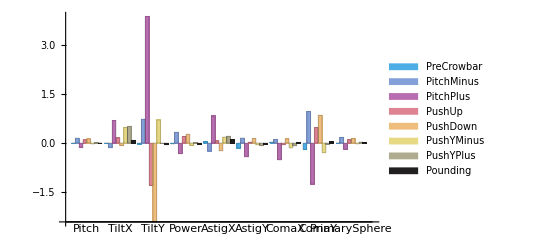

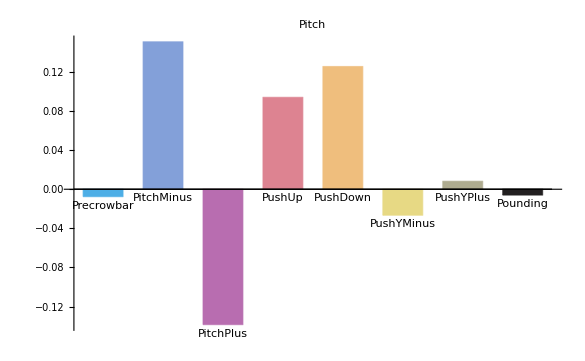

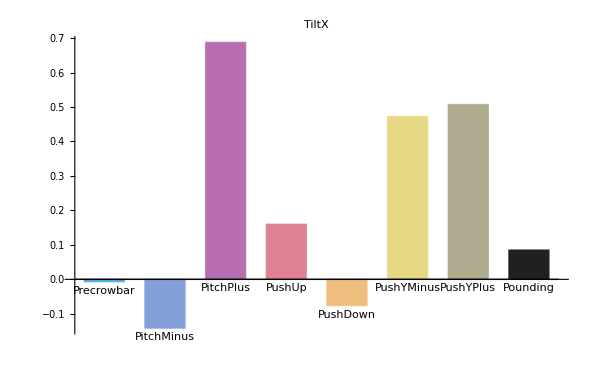

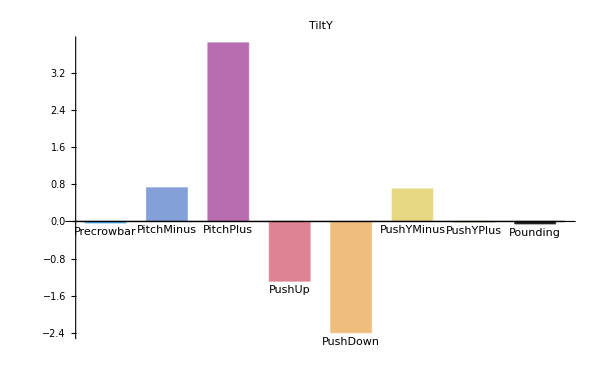

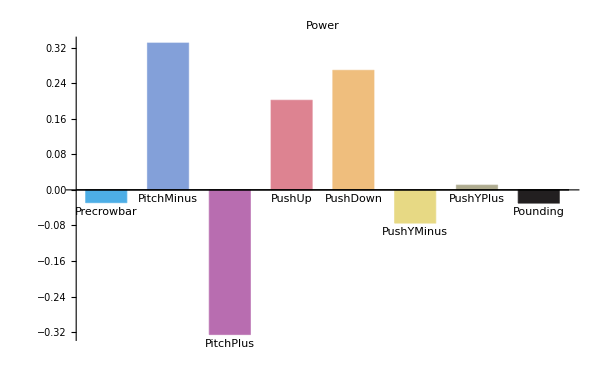

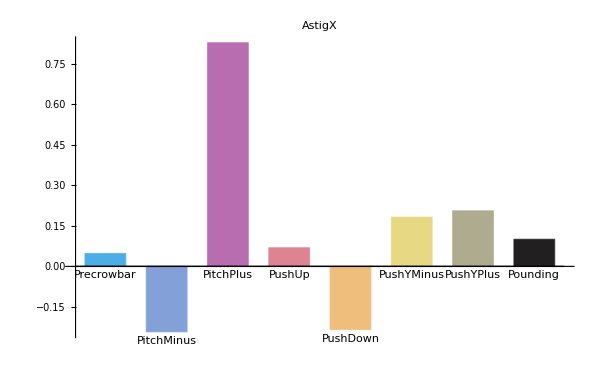

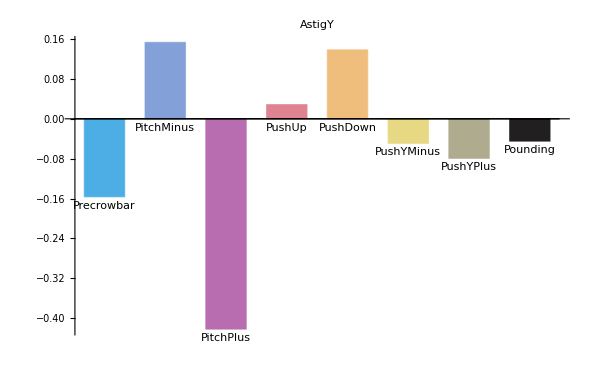

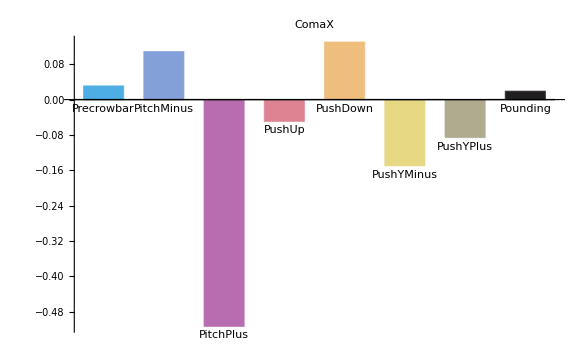

```mathematica
BarChart[{pi,tx,ty,pw,ax,ay,cx,cy,ps},ChartStyle->"CMYKColors",ChartLegends->{"PreCrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},ChartLabels->{{"Pitch","TiltX","TiltY","Power","AstigX","AstigY","ComaX","ComaY","PrimarySphere"},None},BarSpacing->{Automatic,0.7}]
BarChart[pi,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"Pitch",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[tx,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"TiltX",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[ty,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"TiltY",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[pw,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"Power",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[ax,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"AstigX",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[ay,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"AstigY",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[cx,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"ComaX",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[cy,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"ComaY",BarSpacing->Large,ChartStyle->"CMYKColors"]
BarChart[ps,ChartLabels->Placed[{"Precrowbar","PitchMinus","PitchPlus","PushUp","PushDown","PushYMinus","PushYPlus","Pounding"},Below],PlotLabel->"PrimarySpherical",BarSpacing->Large,ChartStyle->"CMYKColors"]
```